VQCDThermo numerical data analysis tutorial

This notebook contains a simple example on how to analyze the data generated by ComputeStandardThermo, in order to produce an overview of the phase structure of the system, and the necessary information to deduce a detailed phase diagram.

A tutorial to computing the data can be found in ThermoComputationTutorial.nb, which also details the potential and parameters that the data corresponds to.

As usual, we start by loading the package:

```mathematica
Needs["VQCDThermo`"]
```

Then load the thermodata in to a list, of course replacing the path with a path to your data directrory.

The example data can be downloaded from http://users.jyu.fi/~tisaalho/VQCDThermoExampleData.zip

```mathematica
thermo = LoadThermoDirectory["DirectoryForData"];
```

Loading file DirectoryForData/lahconstant1036727150804631353.m

Loading file DirectoryForData/lahconstant1294655432049213536.m

Loading file DirectoryForData/lahconstant3072274136014580908.m

Loading file DirectoryForData/lahconstant327144199006907434.m

Loading file DirectoryForData/lahconstant3330316776053094031.m

Loading file DirectoryForData/lahconstant37131535844070559.m

Loading file DirectoryForData/lahconstant387528594662885164.m

Loading file DirectoryForData/lahconstant3953125887638211342.m

Loading file DirectoryForData/lahconstant402890598583293307.m

Loading file DirectoryForData/lahconstant4187727482314921831.m

Loading file DirectoryForData/lahconstant4396260513555824704.m

Loading file DirectoryForData/lahconstant4465365595008027286.m

Loading file DirectoryForData/lahconstant4490767362423187827.m

Loading file DirectoryForData/lahconstant4726724441685066616.m

Loading file DirectoryForData/lahconstant4955580363659785976.m

Loading file DirectoryForData/lahconstant568792176546679605.m

Loading file DirectoryForData/lahconstant5900745350422362149.m

Loading file DirectoryForData/lahconstant6050563033158725266.m

Loading file DirectoryForData/lahconstant6383466660745292161.m

Loading file DirectoryForData/lahconstant6639406024784707512.m

Loading file DirectoryForData/lahconstant7180366418433142164.m

Loading file DirectoryForData/lahconstant7367478903055640202.m

Loading file DirectoryForData/lahconstant7391207656374431479.m

Loading file DirectoryForData/lahconstant8171782997856170298.m

Loading file DirectoryForData/lahconstant8423184305668784886.m

Loading file DirectoryForData/lahconstant8723754913707105856.m

Loading file DirectoryForData/lahconstanttauh1007325326315333339.m

Loading file DirectoryForData/lahconstanttauh1209216243511080697.m

Loading file DirectoryForData/lahconstanttauh1487675466617798933.m

Loading file DirectoryForData/lahconstanttauh1696975284841042717.m

Loading file DirectoryForData/lahconstanttauh1757341138542462560.m

Loading file DirectoryForData/lahconstanttauh1793939514292105500.m

Loading file DirectoryForData/lahconstanttauh2297466076195081824.m

Loading file DirectoryForData/lahconstanttauh2532436217900043574.m

Loading file DirectoryForData/lahconstanttauh2631802259713631592.m

Loading file DirectoryForData/lahconstanttauh3103497519738964603.m

Loading file DirectoryForData/lahconstanttauh3496365340060519013.m

Loading file DirectoryForData/lahconstanttauh4838480172174448905.m

Loading file DirectoryForData/lahconstanttauh499941506770739498.m

Loading file DirectoryForData/lahconstanttauh5323252606803126396.m

Loading file DirectoryForData/lahconstanttauh5596020536787772557.m

Loading file DirectoryForData/lahconstanttauh591797911696386933.m

Loading file DirectoryForData/lahconstanttauh6805896133261124056.m

Loading file DirectoryForData/lahconstanttauh7578800002909798206.m

Loading file DirectoryForData/lahconstanttauh7709341721998504827.m

Loading file DirectoryForData/lahconstanttauh865323396653669400.m

Loading file DirectoryForData/lahconstanttauh8778957004449782438.m

Loading file DirectoryForData/ntconstant1122199531469212949.m

Loading file DirectoryForData/ntconstant1180374837433400624.m

Loading file DirectoryForData/ntconstant1180674594667011234.m

Loading file DirectoryForData/ntconstant146251026830804823.m

Loading file DirectoryForData/ntconstant148599154149473938.m

Loading file DirectoryForData/ntconstant1847461029803808098.m

Loading file DirectoryForData/ntconstant2172341966685679417.m

Loading file DirectoryForData/ntconstant2226066782097666141.m

Loading file DirectoryForData/ntconstant2469031335334587072.m

Loading file DirectoryForData/ntconstant2948388371862675769.m

Loading file DirectoryForData/ntconstant3068859448412189586.m

Loading file DirectoryForData/ntconstant3278048314896656911.m

Loading file DirectoryForData/ntconstant3285327471754738107.m

Loading file DirectoryForData/ntconstant3334920846802033618.m

Loading file DirectoryForData/ntconstant3513543432020038220.m

Loading file DirectoryForData/ntconstant3552156339850739200.m

Loading file DirectoryForData/ntconstant3762332937717319355.m

Loading file DirectoryForData/ntconstant3925416665931882948.m

Loading file DirectoryForData/ntconstant3981424478204652746.m

Loading file DirectoryForData/ntconstant4212692128329192629.m

Loading file DirectoryForData/ntconstant4370698646847565421.m

Loading file DirectoryForData/ntconstant5614648824334343729.m

Loading file DirectoryForData/ntconstant5653103627617146687.m

Loading file DirectoryForData/ntconstant566585984832003589.m

Loading file DirectoryForData/ntconstant6032256531547393240.m

Loading file DirectoryForData/ntconstant6295150849858330482.m

Loading file DirectoryForData/ntconstant6645158415084086928.m

Loading file DirectoryForData/ntconstant7142085672159752843.m

Loading file DirectoryForData/ntconstant7792264496778621710.m

Loading file DirectoryForData/ntconstant8688759362258439448.m

Loading file DirectoryForData/ntconstanttauh1042720171474536614.m

Loading file DirectoryForData/ntconstanttauh125913214361185654.m

Loading file DirectoryForData/ntconstanttauh2510067075343543366.m

Loading file DirectoryForData/ntconstanttauh2695841931246005942.m

Loading file DirectoryForData/ntconstanttauh2793635512367816511.m

Loading file DirectoryForData/ntconstanttauh3598290853696209748.m

Loading file DirectoryForData/ntconstanttauh4239938475974629609.m

Loading file DirectoryForData/ntconstanttauh4754079558751600979.m

Loading file DirectoryForData/ntconstanttauh5147409727169825081.m

Loading file DirectoryForData/ntconstanttauh5268169143567905431.m

Loading file DirectoryForData/ntconstanttauh6206949805670885786.m

Loading file DirectoryForData/ntconstanttauh649933144559662404.m

Loading file DirectoryForData/ntconstanttauh6853834603290886297.m

Loading file DirectoryForData/ntconstanttauh705103299497799064.m

Loading file DirectoryForData/ntconstanttauh7572859008267317980.m

Loading file DirectoryForData/ntconstanttauh768680196744259782.m

thermo is just an ordinary list, so if you have your data split across several directories, you can just Join[thermo1, thermo2]

The structure of each element of thermo is rather complicated, and contains essentially the raw data. The primary helper to convert this to a more easily manageable form is MakeThermoGrid. The next cell takes about 5-10 minutes to run, although you can save about a third of that by making the command MakeThermoGrid[thermo, False], which prevents generating the plots.

The return values λhfuns, ntfuns, λhτhfuns and ntτhfuns are associative arrays for curves of constant nt as a function λh, curves of constant λh as a function of nt, and the same for the broken phase, respectively:

Making thermo ntconstantτh = 0.

Zeroes of pressure found: {3.21173}

Making thermo λhconstantτh = 1.69224

Zeroes of pressure found: {}

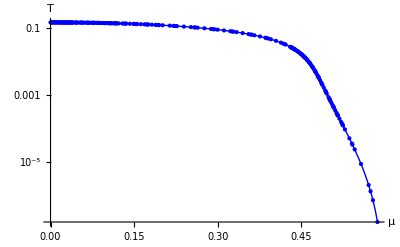

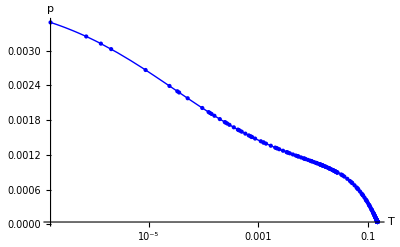

Making thermo λhconstantτh = 2.93115

Zeroes of pressure found: {}

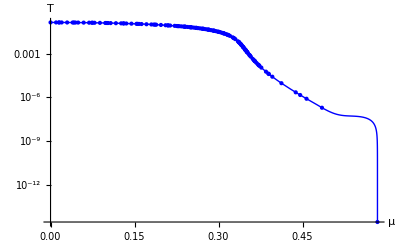

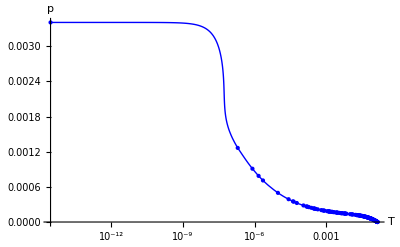

Making thermo λhconstantτh = 5.07709

Zeroes of pressure found: {4.30318}

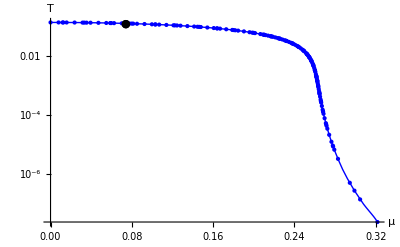

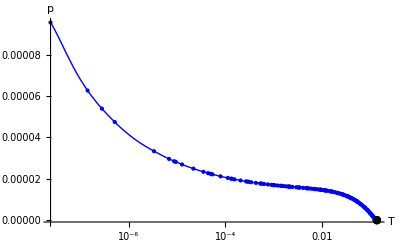

Making thermo λhconstantτh = 8.79411

Zeroes of pressure found: {10.0259, 23.4777}

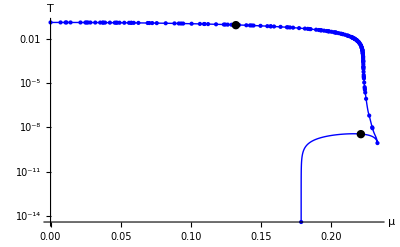

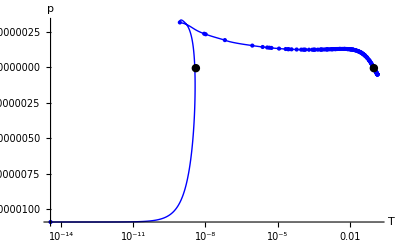

Making thermo λhconstantτh = 15.2324

Zeroes of pressure found: {}

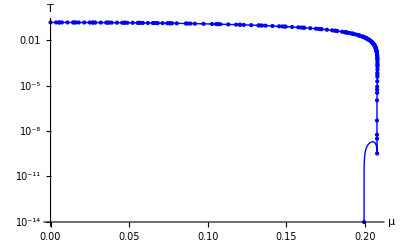

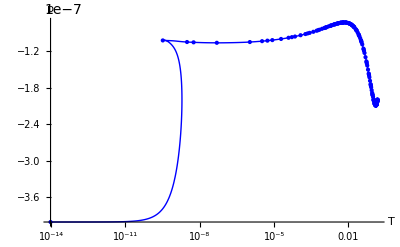

Making thermo λhconstantτh = 26.3843

Zeroes of pressure found: {}

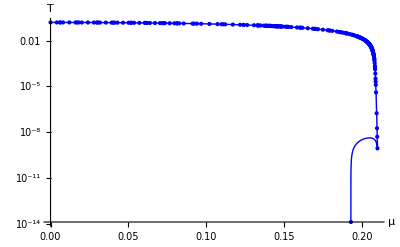

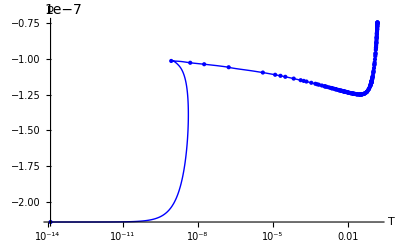

Making thermo λhconstantτh = 45.7007

Zeroes of pressure found: {24.61, 24.658}

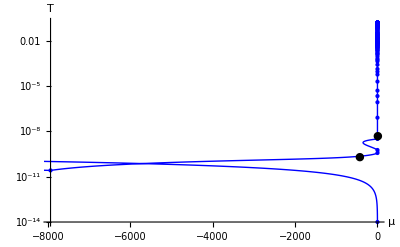

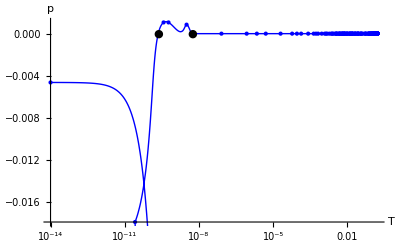

Making thermo λhconstantτh = 79.1589

Zeroes of pressure found: {23.3541, 23.4113}

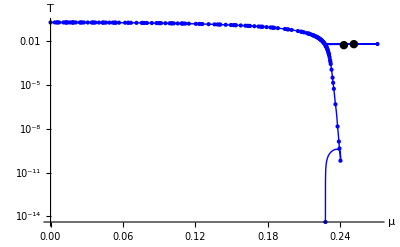

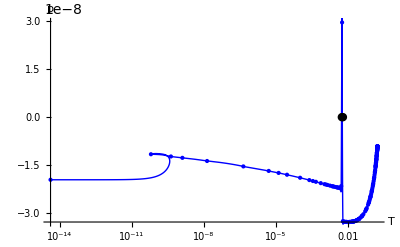

Making thermo λhconstantτh = 137.112

Zeroes of pressure found: {}

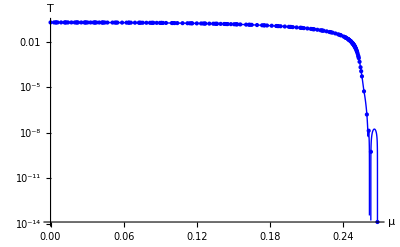

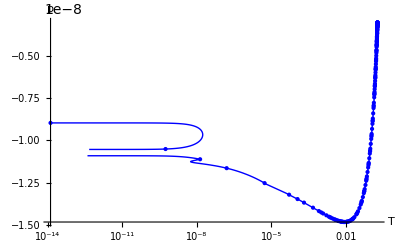

Making thermo λhconstantτh = 237.495

Zeroes of pressure found: {}

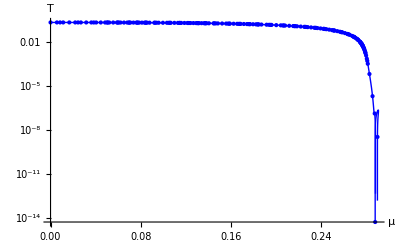

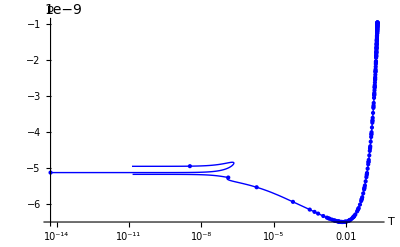

Making thermo λhconstantτh = 411.368

Zeroes of pressure found: {}

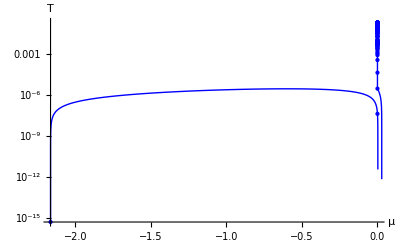

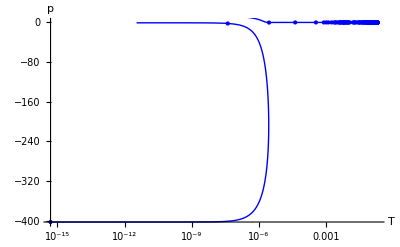

Making thermo λhconstantτh = 712.537

Zeroes of pressure found: {}

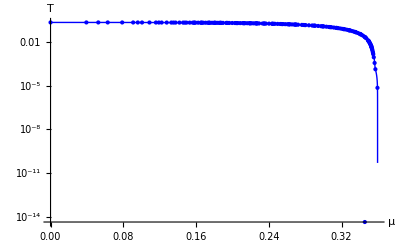

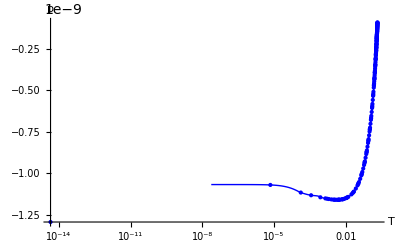

Making thermo λhconstantτh = 1234.2

Zeroes of pressure found: {}

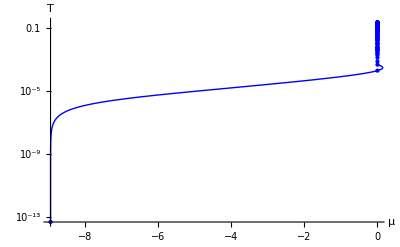

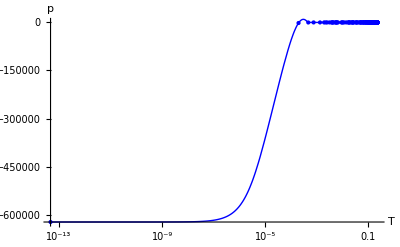

Making thermo λhconstantτh = 2137.77

Zeroes of pressure found: {}

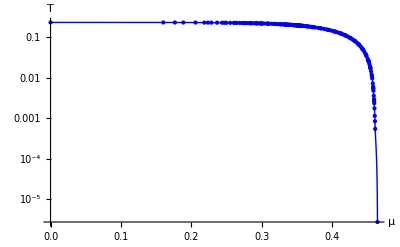

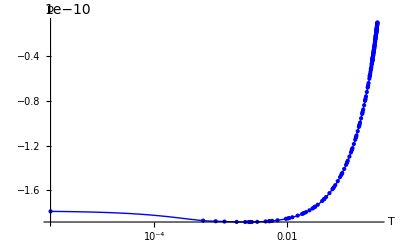

Making thermo λhconstantτh = 3702.87

Zeroes of pressure found: {}

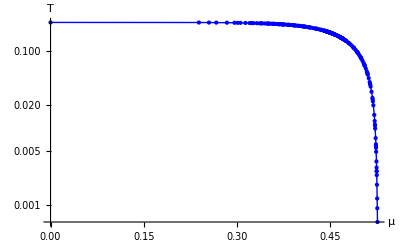

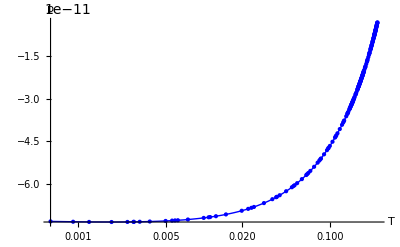

Making thermo λhconstantτh = 6413.8

Zeroes of pressure found: {}

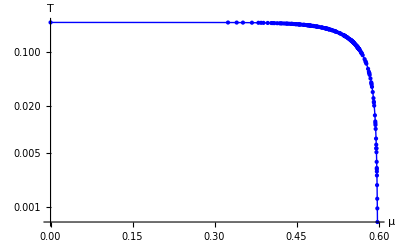

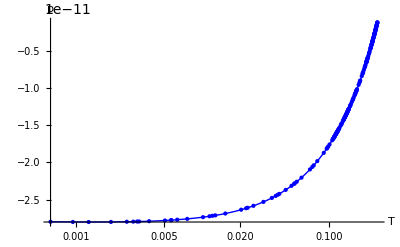

Making thermo λhconstantτh = 11109.4

Zeroes of pressure found: {}

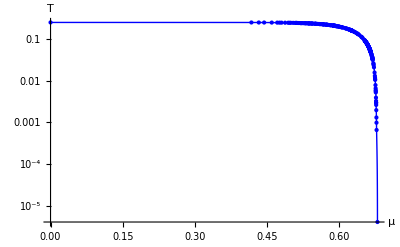

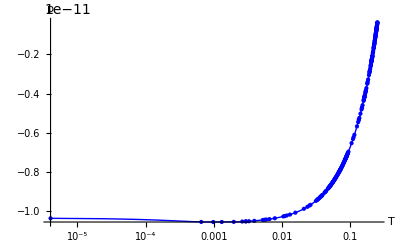

Making thermo λhconstantτh = 19242.8

Zeroes of pressure found: {}

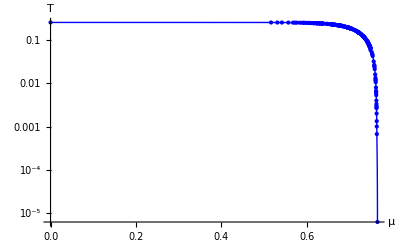

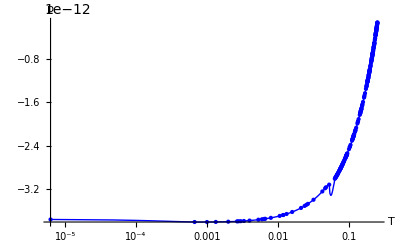

Making thermo λhconstantτh = 33330.8

Zeroes of pressure found: {}

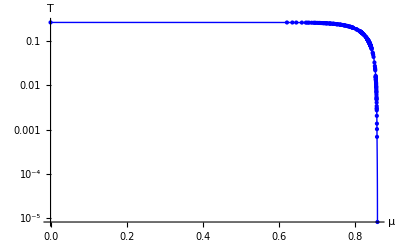

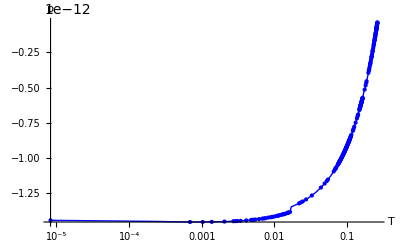

Making thermo λhconstantτh = 57732.9

Zeroes of pressure found: {}

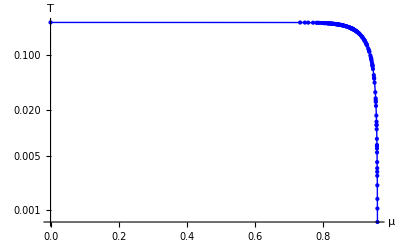

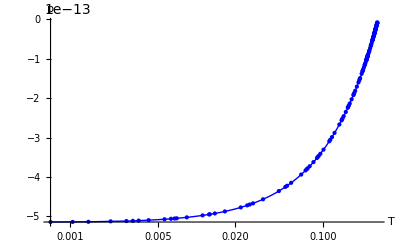

Making thermo λhconstantτh = 100000.

Zeroes of pressure found: {0.14335}

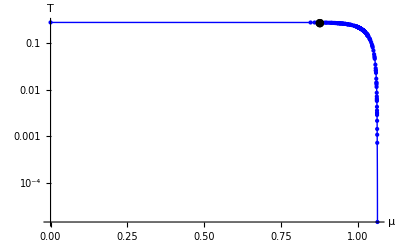

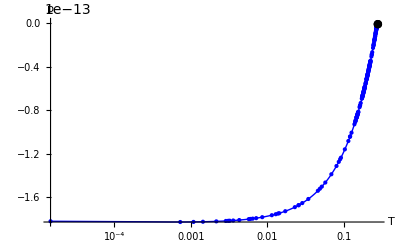

Making thermo ntconstant = 0.

Zeroes of pressure found: {1.69883}

Making thermo λhconstant = 0.01

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

Zeroes of pressure found: {10.3992}

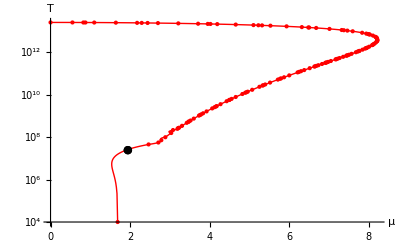

-Graphics-

Making thermo λhconstant = 0.0119042

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

Zeroes of pressure found: {10.3894}

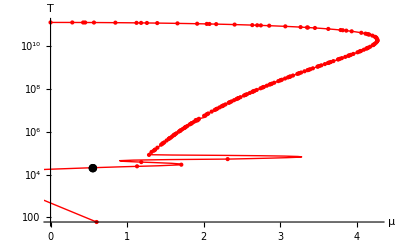

-Graphics-

Making thermo λhconstant = 0.014171

Zeroes of pressure found: {}

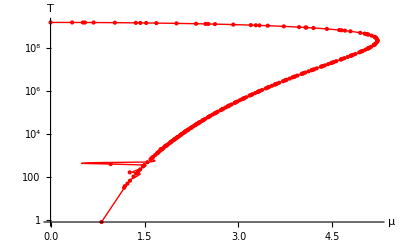

-Graphics-

Making thermo λhconstant = 0.0168694

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

General::stop: Further output of FindRoot :: brmp will be suppressed during this calculation.

Zeroes of pressure found: {10.3653}

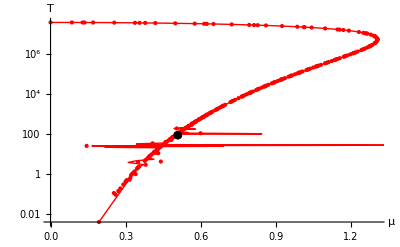

-Graphics-

Making thermo λhconstant = 0.0200816

Zeroes of pressure found: {}

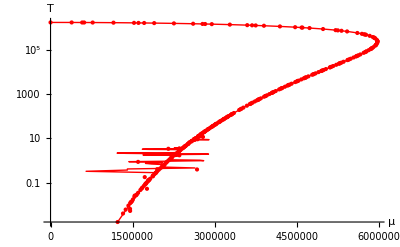

-Graphics-

Making thermo λhconstant = 0.0239055

Zeroes of pressure found: {}

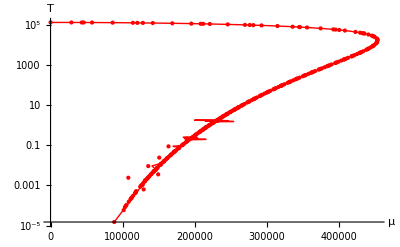

-Graphics-

Making thermo λhconstant = 0.0284575

Zeroes of pressure found: {}

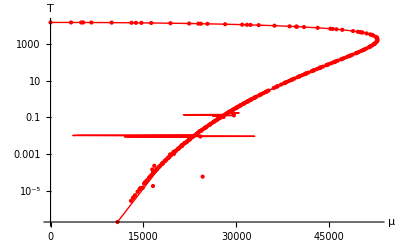

-Graphics-

Making thermo λhconstant = 0.0338764

Zeroes of pressure found: {}

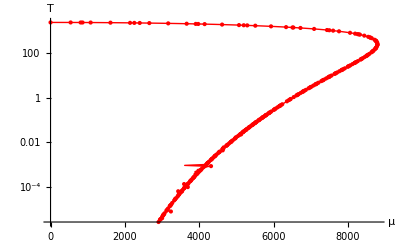

-Graphics-

Making thermo λhconstant = 0.0403271

Zeroes of pressure found: {10.2807, 10.2807, 10.2807}

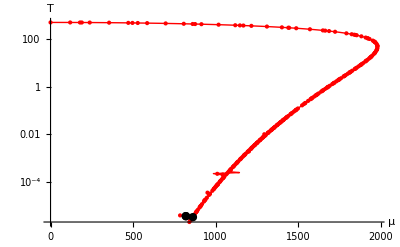

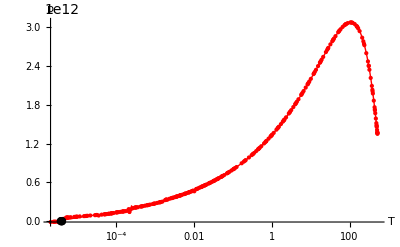

Making thermo λhconstant = 0.0480061

Zeroes of pressure found: {}

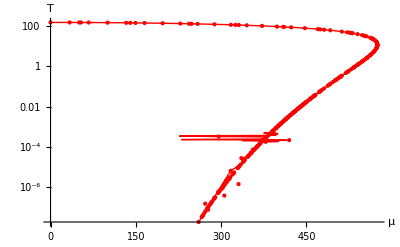

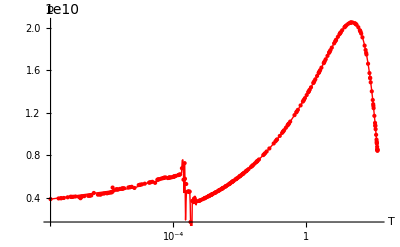

Making thermo λhconstant = 0.0571473

Zeroes of pressure found: {}

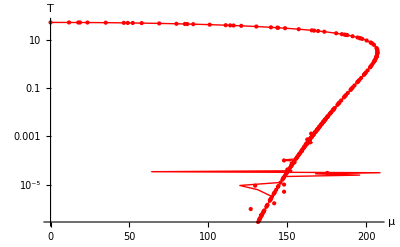

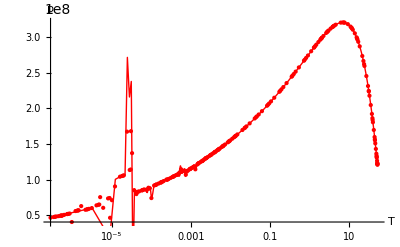

Making thermo λhconstant = 0.0680292

Zeroes of pressure found: {10.2319, 10.2319, 10.2319, 10.2319, 10.2319, 10.232, 10.232, 10.232}

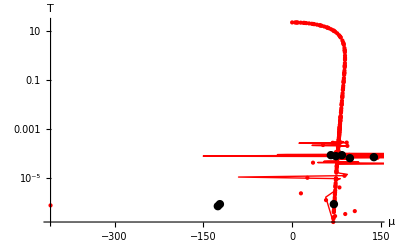

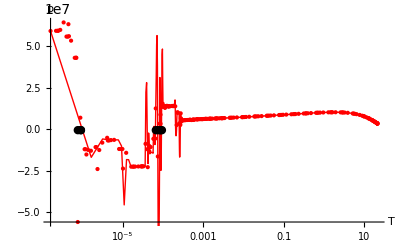

Making thermo λhconstant = 0.0809832

Zeroes of pressure found: {}

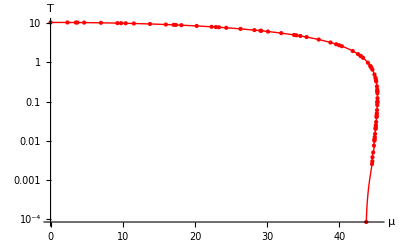

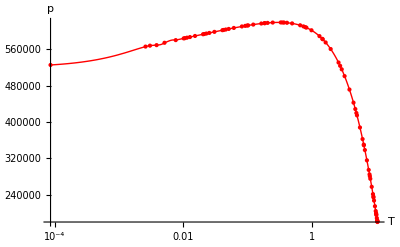

Making thermo λhconstant = 0.0964038

Zeroes of pressure found: {10.2248, 10.2249, 10.2249, 10.2249, 10.2249, 10.2249, 10.2249, 10.225, 10.225, 10.225}

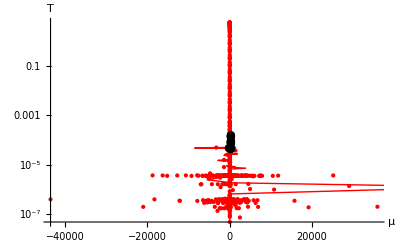

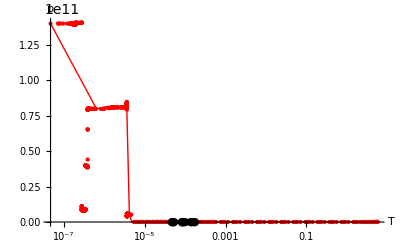

Making thermo λhconstant = 0.114761

Zeroes of pressure found: {10.2379}

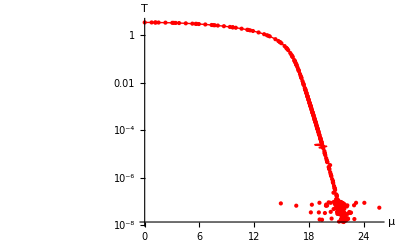

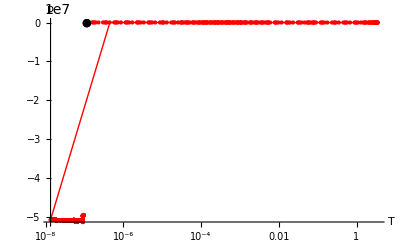

Making thermo λhconstant = 0.136613

Zeroes of pressure found: {}

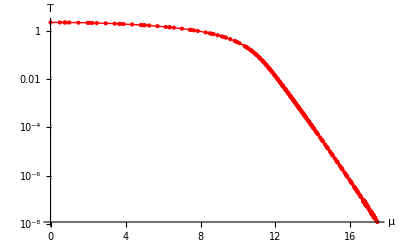

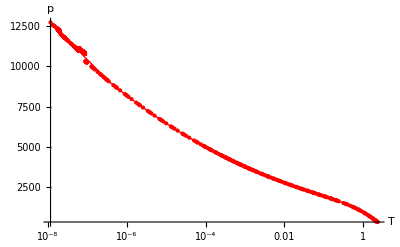

Making thermo λhconstant = 0.162627

Zeroes of pressure found: {}

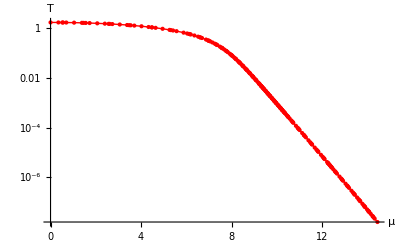

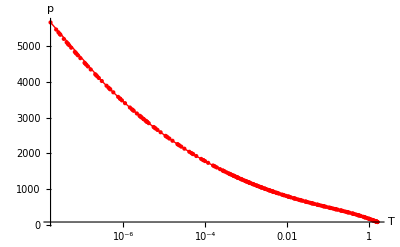

Making thermo λhconstant = 0.230458

Zeroes of pressure found: {10.4926}

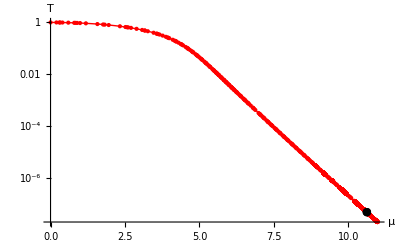

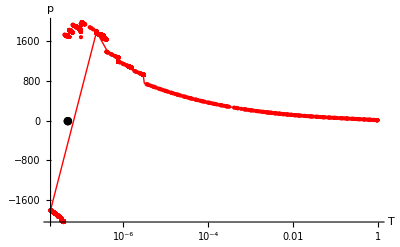

Making thermo λhconstant = 0.274342

Zeroes of pressure found: {}

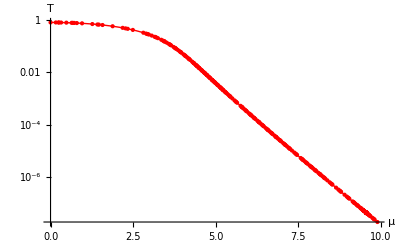

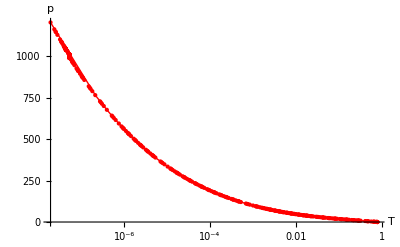

Making thermo λhconstant = 0.462797

Zeroes of pressure found: {}

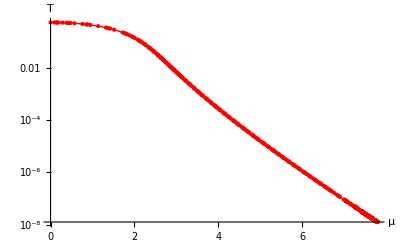

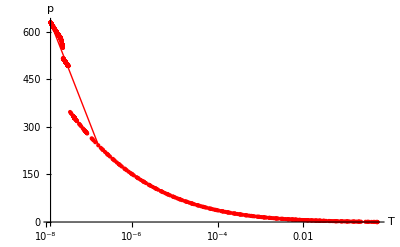

Making thermo λhconstant = 0.655827

Zeroes of pressure found: {}

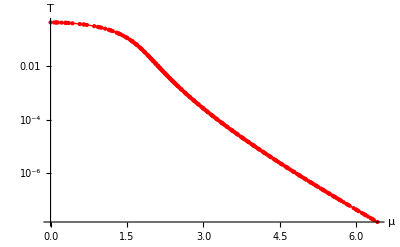

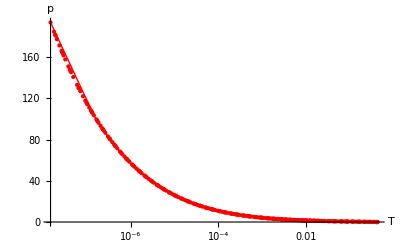

Making thermo λhconstant = 0.780709

Zeroes of pressure found: {}

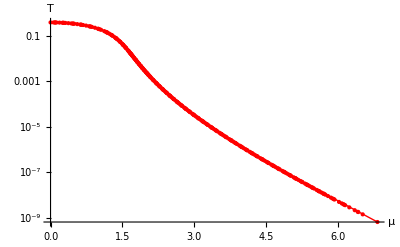

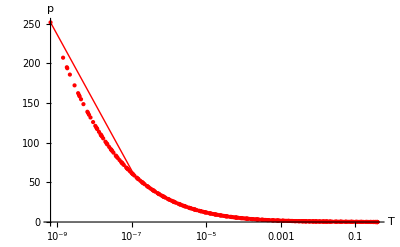

Making thermo λhconstant = 0.92937

Zeroes of pressure found: {}

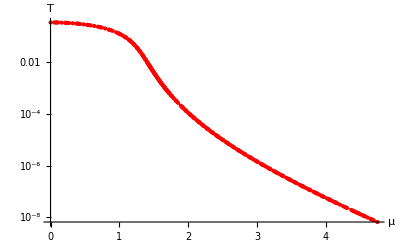

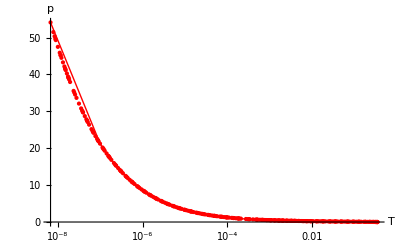

Making thermo λhconstant = 1.31701

Zeroes of pressure found: {12.0468}

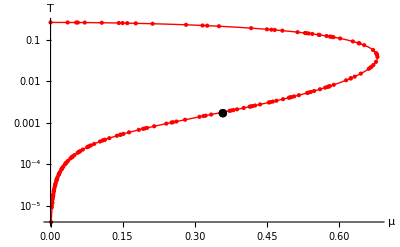

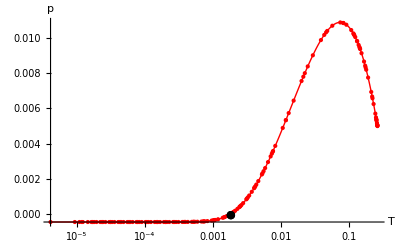

Making thermo λhconstant = 1.56779

Zeroes of pressure found: {9.9719}

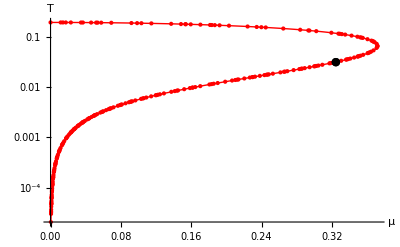

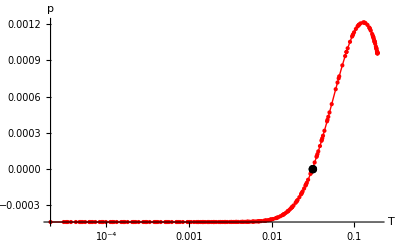

Making thermo λhconstant = 1.86632

Zeroes of pressure found: {}

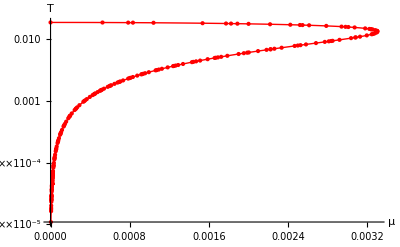

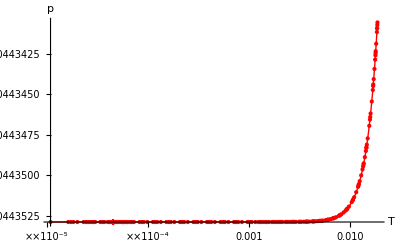

Making thermo ntconstantτh = 0.226102

Zeroes of pressure found: {3.21934}

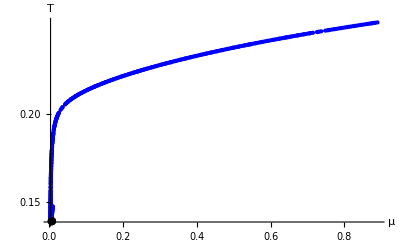

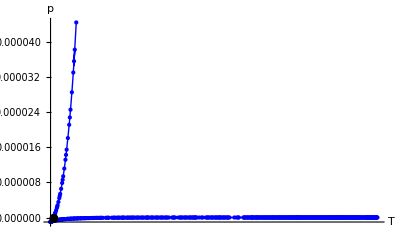

Making thermo ntconstantτh = 0.50873

Zeroes of pressure found: {3.25099}

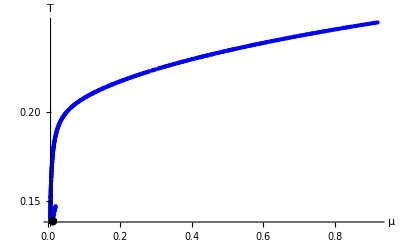

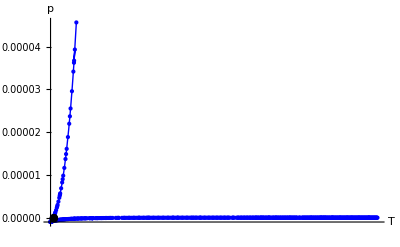

Making thermo ntconstantτh = 0.904409

Zeroes of pressure found: {3.33273}

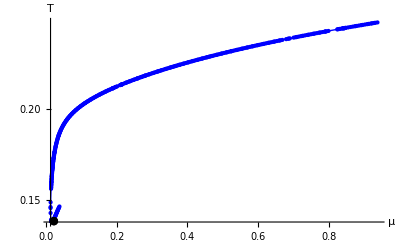

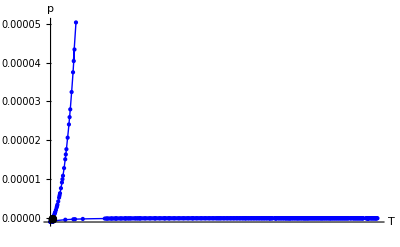

Making thermo ntconstantτh = 1.41314

Zeroes of pressure found: {3.4968}

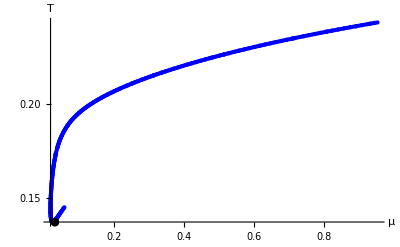

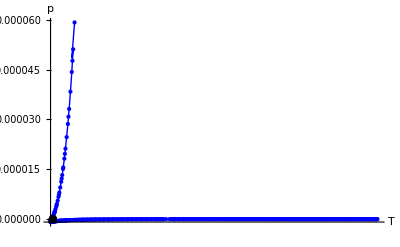

Making thermo ntconstantτh = 2.76975

Zeroes of pressure found: {4.13528}

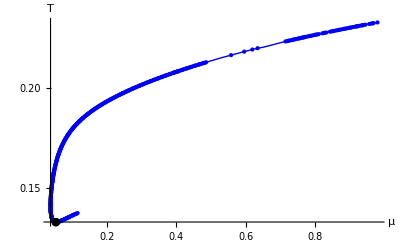

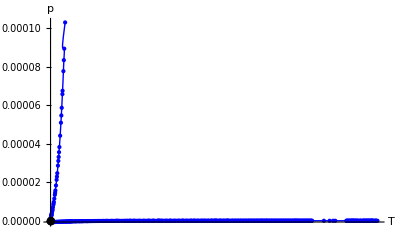

Making thermo ntconstantτh = 3.61764

Zeroes of pressure found: {4.63922, 20088.6, 20181.5}

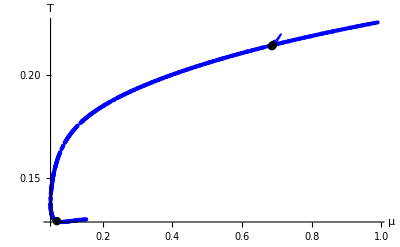

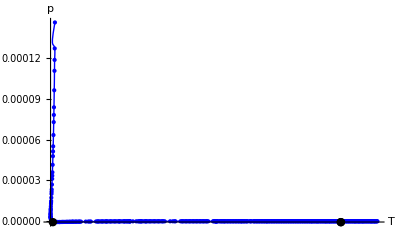

Making thermo ntconstantτh = 5.65256

Zeroes of pressure found: {5.97316}

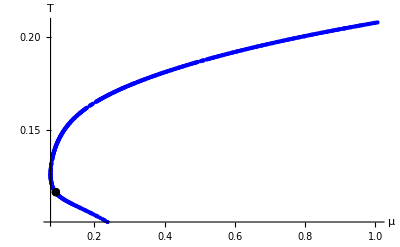

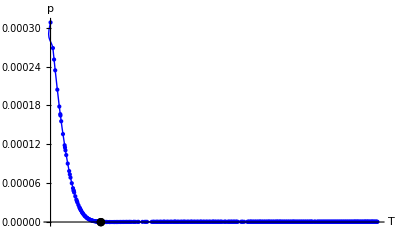

Making thermo ntconstantτh = 6.83959

Zeroes of pressure found: {6.71583}

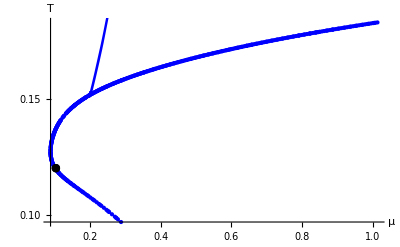

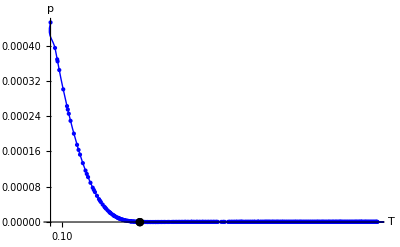

Making thermo ntconstantτh = 8.13968

Zeroes of pressure found: {7.61779}

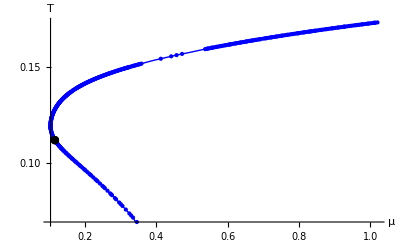

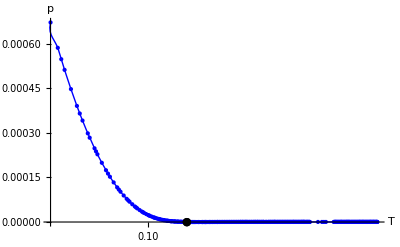

Making thermo ntconstantτh = 9.55282

Zeroes of pressure found: {8.50335}

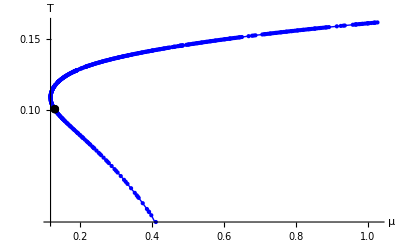

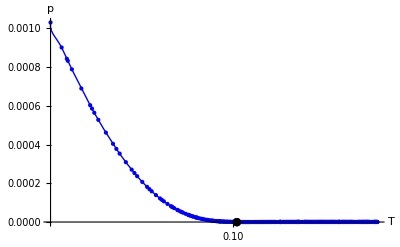

Making thermo ntconstantτh = 11.079

Zeroes of pressure found: {9.41366}

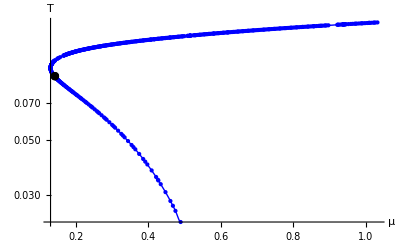

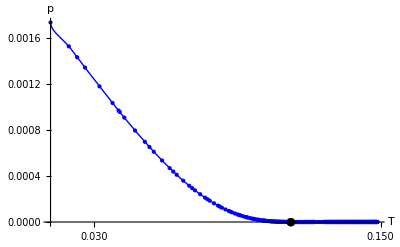

Making thermo ntconstantτh = 14.4705

Zeroes of pressure found: {11.2818, 199.243, 292.413}

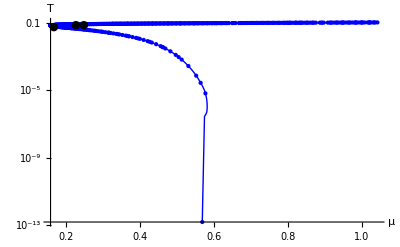

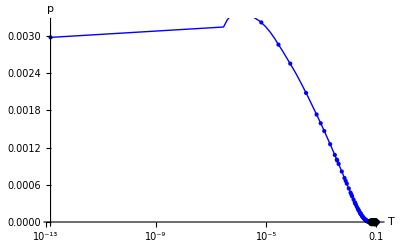

Making thermo ntconstantτh = 16.3359

Zeroes of pressure found: {12.1138}

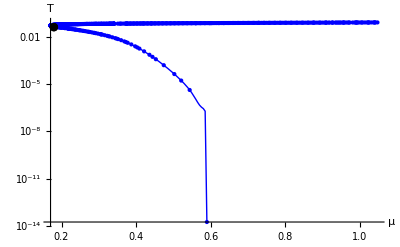

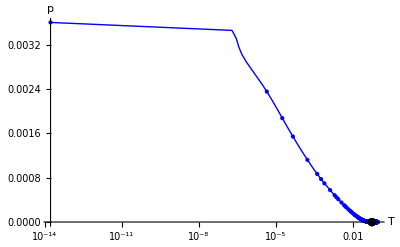

Making thermo ntconstantτh = 20.4057

Zeroes of pressure found: {13.496}

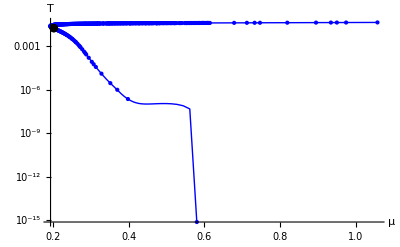

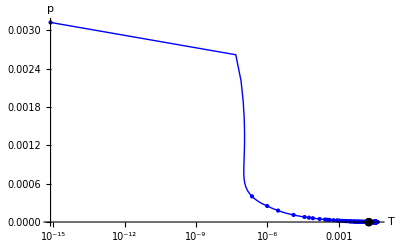

Making thermo ntconstantτh = 22.6102

Zeroes of pressure found: {13.5814}

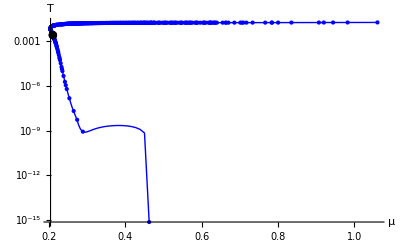

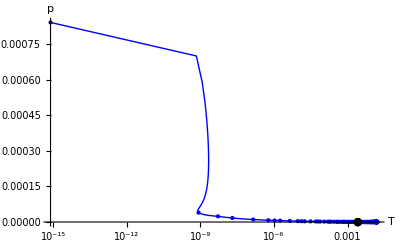

Making thermo ntconstant = 0.0127937

Zeroes of pressure found: {1.69883}

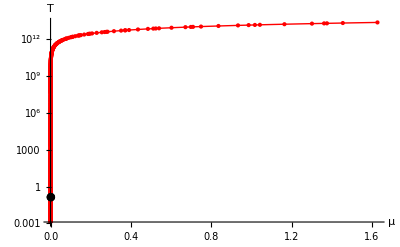

-Graphics-

Making thermo ntconstant = 0.0511748

Zeroes of pressure found: {1.69883}

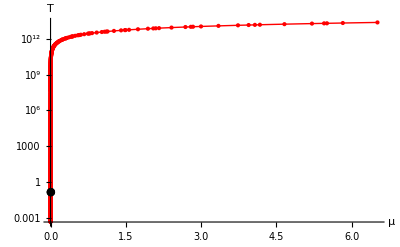

-Graphics-

Making thermo ntconstant = 0.115143

Zeroes of pressure found: {1.69884}

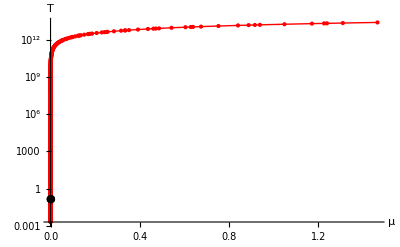

-Graphics-

Making thermo ntconstant = 0.204699

Zeroes of pressure found: {1.69884}

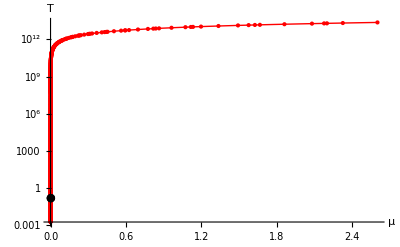

-Graphics-

Making thermo ntconstant = 0.319842

Zeroes of pressure found: {1.69885}

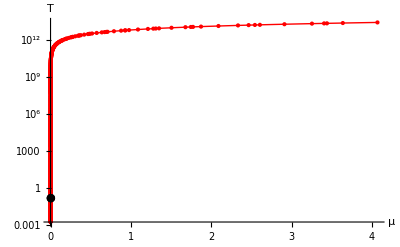

-Graphics-

Making thermo ntconstant = 0.460573

Zeroes of pressure found: {1.69886}

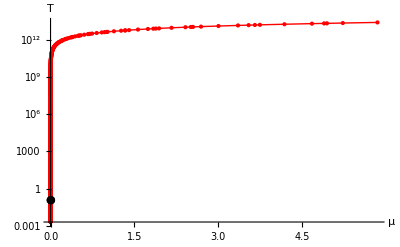

-Graphics-

Making thermo ntconstant = 0.626891

Zeroes of pressure found: {1.69888}

-Graphics-

-Graphics-

Making thermo ntconstant = 0.818797

Zeroes of pressure found: {1.6989}

-Graphics-

-Graphics-

Making thermo ntconstant = 1.03629

Zeroes of pressure found: {1.69894}

-Graphics-

-Graphics-

Making thermo ntconstant = 1.27937

Zeroes of pressure found: {1.69898}

-Graphics-

-Graphics-

Making thermo ntconstant = 1.54804

Zeroes of pressure found: {1.69901}

-Graphics-

-Graphics-

Making thermo ntconstant = 1.84229

Zeroes of pressure found: {1.69902}

-Graphics-

-Graphics-

Making thermo ntconstant = 2.16213

Zeroes of pressure found: {1.69898}

-Graphics-

-Graphics-

Making thermo ntconstant = 2.50756

Zeroes of pressure found: {1.69888}

-Graphics-

-Graphics-

Making thermo ntconstant = 2.87858

Zeroes of pressure found: {1.6986}

-Graphics-

-Graphics-

Making thermo ntconstant = 3.27519

Zeroes of pressure found: {1.69811}

-Graphics-

-Graphics-

Making thermo ntconstant = 3.69738

Zeroes of pressure found: {1.69725}

-Graphics-

-Graphics-

Making thermo ntconstant = 4.14516

Zeroes of pressure found: {1.69589}

-Graphics-

-Graphics-

Making thermo ntconstant = 4.61852

Zeroes of pressure found: {1.69383}

-Graphics-

-Graphics-

Making thermo ntconstant = 5.11748

Zeroes of pressure found: {1.6908}

-Graphics-

-Graphics-

Making thermo ntconstant = 5.64202

Zeroes of pressure found: {1.68651}

-Graphics-

-Graphics-

Making thermo ntconstant = 6.76787

Zeroes of pressure found: {1.67239}

-Graphics-

-Graphics-

Making thermo ntconstant = 7.36917

Zeroes of pressure found: {1.66138}

-Graphics-

-Graphics-

Making thermo ntconstant = 7.99606

Zeroes of pressure found: {1.64667}

-Graphics-

-Graphics-

Making thermo ntconstant = 8.64854

Zeroes of pressure found: {1.62702}

-Graphics-

-Graphics-

Making thermo ntconstant = 9.32661

Zeroes of pressure found: {1.6006}

-Graphics-

-Graphics-

Making thermo ntconstant = 10.0303

Zeroes of pressure found: {1.56435}

-Graphics-

-Graphics-

Making thermo ntconstant = 10.7595

Zeroes of pressure found: {1.51233}

-Graphics-

-Graphics-

Making thermo ntconstant = 11.5143

Zeroes of pressure found: {1.42885}

-Graphics-

-Graphics-

{287.67259,{{VQCDThermo`Private`out$10484,VQCDThermo`Private`out$30315,VQCDThermo`Private`out$30826,VQCDThermo`Private`out$31337,VQCDThermo`Private`out$31848,VQCDThermo`Private`out$32359,VQCDThermo`Private`out$32870,VQCDThermo`Private`out$33381,VQCDThermo`Private`out$33892,VQCDThermo`Private`out$34403,VQCDThermo`Private`out$34914,VQCDThermo`Private`out$35425,VQCDThermo`Private`out$35936,VQCDThermo`Private`out$36447,VQCDThermo`Private`out$36958,VQCDThermo`Private`out$37469,VQCDThermo`Private`out$37980,VQCDThermo`Private`out$38491,VQCDThermo`Private`out$39002,VQCDThermo`Private`out$39513,VQCDThermo`Private`out$40028,VQCDThermo`Private`out$40539,VQCDThermo`Private`out$41050,VQCDThermo`Private`out$41561,VQCDThermo`Private`out$42072,VQCDThermo`Private`out$42583,VQCDThermo`Private`out$43094,VQCDThermo`Private`out$43605,VQCDThermo`Private`out$44116,VQCDThermo`Private`out$44627},{VQCDThermo`Private`out$10490,VQCDThermo`Private`out$11431,VQCDThermo`Private`out$12362,VQCDThermo`Private`out$12763,VQCDThermo`Private`out$13915,VQCDThermo`Private`out$14308,VQCDThermo`Private`out$14765,VQCDThermo`Private`out$15222,VQCDThermo`Private`out$15619,VQCDThermo`Private`out$16068,VQCDThermo`Private`out$16529,VQCDThermo`Private`out$16926,VQCDThermo`Private`out$17385,VQCDThermo`Private`out$17838,VQCDThermo`Private`out$18301,VQCDThermo`Private`out$18752,VQCDThermo`Private`out$19153,VQCDThermo`Private`out$19554,VQCDThermo`Private`out$20005,VQCDThermo`Private`out$20406,VQCDThermo`Private`out$20807,VQCDThermo`Private`out$21208,VQCDThermo`Private`out$21609,VQCDThermo`Private`out$22010,VQCDThermo`Private`out$22457,VQCDThermo`Private`out$22904},{VQCDThermo`Private`out$1711,VQCDThermo`Private`out$23346,VQCDThermo`Private`out$23803,VQCDThermo`Private`out$24260,VQCDThermo`Private`out$24717,VQCDThermo`Private`out$25174,VQCDThermo`Private`out$25631,VQCDThermo`Private`out$26090,VQCDThermo`Private`out$26547,VQCDThermo`Private`out$27004,VQCDThermo`Private`out$27461,VQCDThermo`Private`out$27918,VQCDThermo`Private`out$28369,VQCDThermo`Private`out$28950,VQCDThermo`Private`out$29405,VQCDThermo`Private`out$29860},{VQCDThermo`Private`out$1718,VQCDThermo`Private`out$2275,VQCDThermo`Private`out$2680,VQCDThermo`Private`out$3072,VQCDThermo`Private`out$3529,VQCDThermo`Private`out$3934,VQCDThermo`Private`out$4339,VQCDThermo`Private`out$4794,VQCDThermo`Private`out$5249,VQCDThermo`Private`out$5654,VQCDThermo`Private`out$6059,VQCDThermo`Private`out$6464,VQCDThermo`Private`out$6869,VQCDThermo`Private`out$7398,VQCDThermo`Private`out$7859,VQCDThermo`Private`out$8188,VQCDThermo`Private`out$8517,VQCDThermo`Private`out$8914,VQCDThermo`Private`out$9311,VQCDThermo`Private`out$9708,VQCDThermo`Private`out$10037}}}

```mathematica
Timing[{λhfuns, ntfuns, λhτhfuns, ntτhfuns} = MakeThermoGrid[thermo]]
```

And now we’re good to go with the plotting! Each opf λhτhfuns, ntτhfuns, λhfuns, ntfuns is simply a list of associative arrays containing the results. Let’s see the plots first, and then follow it with a simple tutorial on extracting the various elements:

```mathematica
Show[(ParametricPlot[{#[μ][x], #[T][x]}, {x, #[min], #[max]}, AspectRatio -> 1 , PlotStyle-> Red, PlotRange-> {{0, 2.}, {0, 0.5}}, AxesLabel-> {"μ", "T"}])& /@Select[Join[λhfuns, ntfuns], NumericQ[#[min]]&], (ParametricPlot[{#[μ][x], #[T][x]}, {x, #[min], #[max]}, AspectRatio -> 1 , PlotStyle-> Blue, PlotRange-> {{0, 5.}, {0, 0.5}}, PlotPoints -> 10000])& /@Select[Join[λhτhfuns, ntτhfuns],  NumericQ[#[min]]&]]
```

-Graphics-

As you can see, there are a few numerical fluctuations in these plots. These are also visible in the output during the construction of the thermo functions above. Note though that the long curves extending out from the individual curves are actually interpolation artifacts, typically caused by a single point where the numerics break down. The interpolation then generates the curve between that point and the main curve.

This will force us to also do some manual housekeeping below in order to construct the phase diagram.

Plot the same thing in 3D:

```mathematica
pSB[μf_, Tf_, xf_] :=  Pi^2/45 (1+ 7/4 xf) Tf^4 +1/6 xf μf^2 Tf^2 + 1/ (12 Pi^2) xf μf^4
Show[Plot3D[0, {μ, 0, 0.5}, {T, 0.0, .5}, PlotRange-> {-0.5, 5.0}, AxesLabel-> {"μ", "T", "4 G_5 p/p_SB"}, BoxRatios-> {1, 1, 1}, PlotStyle-> {Purple, Opacity[0.25]}, Mesh-> None], (ParametricPlot3D[{#[μ][x], #[T][x], #[p][x]/pSB[#[μ][x], #[T][x], 1. ]}, {x, #[min], #[max]}, AspectRatio -> 1 , PlotStyle-> Red, PlotRange-> {{0, 2.}, {0, 1.}, {-2, 5}}, BoxRatios -> {1, 1, 1}, AxesLabel-> {"μ", "T", "p/pSB"}])& /@Join[λhfuns, ntfuns], (ParametricPlot3D[{#[μ][x], #[T][x], #[p][x]/pSB[#[μ][x], #[T][x], 1. ]}, {x, #[min], #[max]}, AspectRatio -> 1 , PlotStyle-> Blue, PlotRange-> {{0, 5.}, {0, 1.}, {-1, 5}}, BoxRatios -> {1, 1, 1}, AxesLabel-> {"μ", "T", "p/pSB"}, PlotPoints-> 10000])& /@Join[λhτhfuns, ntτhfuns]]
```

-Graphics3D-

Data on the zeroes of the pressure function is included. These are points where there is a transition between a black hole phase and the vacuum (hadron gas) phase, although further inspection is of course needed to find out which are metastable:

```mathematica
Show[ListPlot[(Function[λh, {#[μ][λh], #[T][λh]}]@First @ #[proots])&/@λhfuns, PlotRange -> {{0, 0.6}, {0, 0.2}}, PlotStyle -> Red, AxesLabel -> {"μ", "T"}], ListPlot[(Function[λh, {#[μ][λh], #[T][λh]}]@First @ #[proots])&/@λhτhfuns, PlotRange -> {{0, 1.1}, {0, 0.2}}, PlotStyle -> Blue], 
ListPlot[(Function[nt, {#[μ][nt], #[T][nt]}]@First @ #[proots])&/@Select[ntτhfuns, Length[#[proots]] > 0&], PlotRange -> {{0, 0.6}, {0, 0.2}}, PlotStyle-> Blue]]
```

-Graphics-

Another potential source for phase transitions is the endpoint of the chirally broken phase curve, which meets the symmetric phase if τh -> 0 at the endpoint:

```mathematica
Show[ListPlot[(Function[λh, {#[μ][λh], #[T][λh]}]@ #[min])&/@λhτhfuns, PlotRange -> {{0, 0.6}, {0, 0.2}}, PlotStyle -> Blue, AxesLabel -> {"μ", "T"}],
ListPlot[(Function[nt, {#[μ][nt], #[T][nt]}]@ #[max])&/@ntτhfuns, PlotRange -> {{0, 0.6}, {0, 0.2}}, PlotStyle -> Blue, AxesLabel -> {"μ", "T"}]]
```

-Graphics-

Okay, so let’s build these into InterpolatingFunctions and plot the phase diagram.

First, we observe, from the 3D plot, that it is the p = 0 -curve in the tachyonic branch which gives the deconfinement transition. Build that as a function of μ:

```mathematica
TdeconfPoints = Select[First @ Thread @ Function[λh, {#[μ][λh], #[T][λh]}][#[proots]]& /@ λhτhfuns, #[[1]] > 0 && #[[2]] > 0&]
```

{{0.00517445,0.141177},{0.0115556,0.140989},{0.0201606,0.140504},{0.0304062,0.139555},{0.0531989,0.135834},{0.0648257,0.132889},{0.088683,0.124142},{0.101439,0.117876},{0.114052,0.11027},{0.127175,0.101042},{0.140333,0.0902493},{0.16589,0.0642953},{0.178167,0.0493332},{0.200314,0.0171773},{0.208893,0.00255577}}

```mathematica
ListPlot[TdeconfPoints]
```

-Graphics-

Make an InterpolatingFunction:

```mathematica
TdeconfFun = Interpolation[TdeconfPoints]
```

InterpolatingFunction[{{0.00517445,0.208893}},<>]

Then build the transition between the chirally symmetric and symmetry breaking phases, part of which is the chiral symmetry restoring transition:

```mathematica
TχPoints = Join[(Function[λh, {#[μ][λh], #[T][λh]}]@ #[min])&/@λhτhfuns, (Function[nt, {#[μ][nt], #[T][nt]}]@ #[max])&/@ntτhfuns];
```

```mathematica
ListPlot[TχPoints]
```

-Graphics-

This needs a little cleanup in the very low T -region:

```mathematica
TχPointsclean = Select[TχPoints, #[[1]] > 0 && #[[2]] > 10^-4&];
```

```mathematica
TχFun = Interpolation[TχPointsclean]
```

InterpolatingFunction[{{0.00949344,0.958309}},<>]

Now plot these in the same plot, and denote the various areas (the warnings and the extra vertical line in the plot seem to be a Mathematica bug):

```mathematica
Show[Plot[Undefined, {x, 0, 0.6}, PlotRange-> {0., .2}, AxesLabel-> {"μ", "T"}], Plot[TχFun[μ], {μ, TχPointsclean[[1, 1]], TχPointsclean[[-1, 1]]}, PlotStyle-> {Blue, Dashed}, Filling -> Top, FillingStyle-> Opacity[.11, Red], PlotRange-> {0, 0.2}], Plot[TdeconfFun[μ], {μ, TdeconfPoints[[1, 1]], TdeconfPoints[[-1, 1]]}, PlotStyle-> Red, PlotRange-> All, Filling -> Bottom, FillingStyle-> Opacity[0.1, Green]],
(*this plot generates the filling in the chirally broken black hole phase*)
Plot[{Max[TdeconfFun[Clip[μ, {TdeconfPoints[[1, 1]], TdeconfPoints[[-1, 1]]}]], 0], Max[TχFun[Clip[μ, {TχPointsclean[[1, 1]], TχPointsclean[[-1, 1]]}]], 0]}, {μ,0., 0.6}, PlotStyle-> None,Filling -> {1 -> {2}}, FillingStyle-> Opacity[0.1, Blue]]
]
```

InterpolatingFunction::dmval: Input value {0.0000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.22449×10^-8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics-

And there we have the phase diagram, labeling the phases is left as an exercise for the reader.

So what are the components of the various curves? Let’s take, say, the second constant nt curve, and dissect it:

```mathematica
curve = λhfuns[[2]]
```

VQCDThermo`Private`out$30315

The basic thermo variables are there as functions of λh, with limits given by curve[min] and curve[max]:

```mathematica
λhmin = curve[min]
λhmax = curve[max]
(*See the values of these functions at λh = 1.1, for example*)
curve[T][1.1]
curve[μ][1.1]
curve[nt] (*nt is constant on this curve, so it doesn't need arguments*)
curve[n][1.1]
curve[Λ][1.1]
curve[Λ][1.1]^(-3) (*4 G5 times the entropy*)
curve[p][1.1]
```

0.01

1.86819

0.312949

0.00112814

0.0127937

0.0002111

1.68953

0.207349

0.012604

The points where p = 0, which are candidates for a transition between the hadron gas phase and one of the black hole phases, are also computed:

```mathematica
curve[proots]
```

{1.69883}

Indeed:

```mathematica
Plot[curve[p][λh], {λh, curve[proots][[1]] - 10^-1, curve[proots][[1]] + 10^-1}, AxesLabel-> {"λh", "p"}, PlotStyle-> Red]
```

-Graphics-

There are also auxiliary variables, such as fscale, τh and the lattice of points where the data is actually computed. The lattice can be used to check if there is doubt as to which wiggles are simply interpolation artifacts

```mathematica
curve[τh][1.1]
curve[fScale][1.1]
curve[lattice]
```

0

1.90481

{0.01,0.0100341,0.0100512,0.0100544,0.0100683,0.0101027,0.0101371,0.0101447,0.0101544,0.0101717,0.0102064,0.0102412,0.0102587,0.0102636,0.0102761,0.0103112,0.0103464,0.0103564,0.010364,0.0103817,0.0104171,0.0104526,0.0104684,0.0104704,0.0104883,0.010524,0.0105599,0.0105666,0.0105779,0.0105959,0.0106321,0.0106683,0.0106865,0.0106959,0.0107047,0.0107412,0.0107779,0.0107962,0.0107986,0.0108146,0.0108515,0.0108885,0.0108957,0.0109071,0.0109257,0.0109629,0.0110003,0.0110191,0.0110279,0.0110379,0.0110755,0.0111133,0.0111321,0.0111322,0.0111512,0.0111892,0.0112274,0.0112338,0.0112465,0.0112657,0.0113041,0.0113427,0.011362,0.0113749,0.0113814,0.0114202,0.0114591,0.0114787,0.0114917,0.0114982,0.0115374,0.0115768,0.0115965,0.0116096,0.0116163,0.0116559,0.0116956,0.0117156,0.0117285,0.0117355,0.0117756,0.0118157,0.0118359,0.0118476,0.011856,0.0118965,0.0119371,0.0119574,0.0119647,0.0119778,0.0120186,0.0120596,0.0120743,0.0120802,0.0121007,0.012142,0.0121834,0.0121953,0.0122042,0.012225,0.0122667,0.0123085,0.012327,0.0123295,0.0123505,0.0123926,0.0124349,0.0124429,0.0124561,0.0124773,0.0125199,0.0125626,0.012584,0.0125947,0.0126054,0.0126484,0.0126916,0.0127132,0.0127149,0.0127349,0.0127783,0.0128219,0.0128296,0.0128437,0.0128656,0.0129095,0.0129535,0.0129756,0.0129887,0.0129977,0.013042,0.0130865,0.0131088,0.0131177,0.0131312,0.0131759,0.0132209,0.013239,0.0132434,0.013266,0.0133112,0.0133566,0.0133669,0.0133794,0.0134022,0.0134479,0.0134938,0.0135168,0.0135223,0.0135398,0.013586,0.0136323,0.0136441,0.0136556,0.0136788,0.0137255,0.0137723,0.0137958,0.0137973,0.0138193,0.0138664,0.0139137,0.0139219,0.0139374,0.0139612,0.0140088,0.0140566,0.0140805,0.0140952,0.0141045,0.0141526,0.0142009,0.0142251,0.0142363,0.0142493,0.0142979,0.0143467,0.0143705,0.0143711,0.0143956,0.0144447,0.014494,0.0145023,0.0145187,0.0145434,0.014593,0.0146428,0.0146678,0.0146842,0.0146928,0.0147429,0.0147932,0.0148184,0.0148343,0.0148436,0.0148942,0.014945,0.0149705,0.0149842,0.014996,0.0150472,0.0150985,0.0151242,0.0151293,0.01515,0.0152017,0.0152535,0.0152652,0.0152795,0.0153055,0.0153577,0.0154101,0.0154364,0.0154429,0.0154627,0.0155154,0.0155684,0.015582,0.0155949,0.0156215,0.0156747,0.0157282,0.015755,0.0157559,0.0157818,0.0158357,0.0158897,0.0158988,0.0159168,0.0159439,0.0159983,0.0160528,0.0160802,0.016098,0.0161076,0.0161625,0.0162177,0.0162453,0.0162621,0.016273,0.0163285,0.0163842,0.0164121,0.0164244,0.0164401,0.0164961,0.0165524,0.0165783,0.0165806,0.0166089,0.0166655,0.0167794,0.0167995,0.0168366,0.016894,0.0170095,0.0171257,0.0171841,0.0172187,0.0172427,0.0173606,0.0174792,0.0175388,0.0175616,0.0175986,0.0177189,0.01784,0.0178867,0.0179008,0.0179619,0.0180846,0.0182082,0.0182389,0.0182703,0.0183326,0.0184579,0.018584,0.0186474,0.0186538,0.018711,0.0188389,0.0189676,0.0189911,0.0190323,0.0190972,0.0192277,0.0193591,0.0194251,0.0194615,0.0194914,0.0196246,0.0197587,0.0198261,0.0198422,0.0198937,0.0200296,0.0201665,0.0202011,0.0202353,0.0203043,0.0204431,0.0205827,0.020653,0.0206581,0.0207234,0.020865,0.0210076,0.0210326,0.0210792,0.0211511,0.0212957,0.0214412,0.0215143,0.0215586,0.0215877,0.0217352,0.0218837,0.0219584,0.0219903,0.0220333,0.0221838,0.0223354,0.0224023,0.0224116,0.0224881,0.0226417,0.0227964,0.0228258,0.0228742,0.0229522,0.0231091,0.023267,0.0233463,0.0233857,0.023426,0.023586,0.0237472,0.0238282,0.0238336,0.0239095,0.0240729,0.0242374,0.024266,0.02432,0.024403,0.0245697,0.0247376,0.024822,0.0248739,0.0249067,0.0250769,0.0252482,0.0253343,0.0253744,0.0254207,0.0255945,0.0257693,0.0258555,0.0258572,0.0259454,0.0261227,0.0263012,0.0263312,0.0263909,0.026481,0.0266619,0.0268441,0.0269357,0.0269965,0.0270275,0.0272122,0.0273982,0.0274916,0.0275524,0.0275854,0.0277739,0.0279637,0.0280591,0.0281159,0.0281548,0.0283472,0.0285409,0.0286382,0.0286766,0.0287359,0.0289323,0.02913,0.0292091,0.0292293,0.029329,0.0295294,0.0297312,0.0297775,0.0298326,0.0299344,0.0301389,0.0303449,0.0304484,0.030471,0.0305522,0.030761,0.0309712,0.0310214,0.0310768,0.0311828,0.0313959,0.0316105,0.0317183,0.0317353,0.0318265,0.0320439,0.0322629,0.0323077,0.032373,0.0324834,0.0327053,0.0329288,0.0330411,0.0330845,0.0331538,0.0333804,0.0336085,0.0336977,0.0337231,0.0338381,0.0340694,0.0345366,0.0346498,0.0347726,0.0350102,0.0354903,0.035977,0.0362228,0.0362579,0.0364703,0.0369705,0.0374775,0.0375782,0.0377336,0.0379914,0.0385124,0.0390405,0.0393073,0.039424,0.0395759,0.0401186,0.0406688,0.0409192,0.0409467,0.0412265,0.0417918,0.0423649,0.0424697,0.0426544,0.0429459,0.0435348,0.0441318,0.0444334,0.0446009,0.044737,0.0453505,0.0459724,0.0462866,0.0463651,0.0466029,0.047242,0.0478898,0.0480594,0.048217,0.0485465,0.0492123,0.0498871,0.050228,0.0502374,0.0505712,0.0512647,0.0519678,0.0520867,0.0523229,0.0526804,0.0534028,0.0541352,0.0545051,0.0547498,0.0548775,0.0556301,0.056393,0.0567783,0.0570229,0.0571663,0.0579502,0.0587449,0.0591464,0.0593595,0.0595505,0.0603672,0.061195,0.0616132,0.0616846,0.0620342,0.0628849,0.0637472,0.0639299,0.0641828,0.0646214,0.0655076,0.0664059,0.0668597,0.0670157,0.0673166,0.0682397,0.0691755,0.0694987,0.0696482,0.0701241,0.0710858,0.0720606,0.0723713,0.072553,0.0730488,0.0740505,0.075066,0.0754452,0.0755789,0.0760954,0.0771389,0.0792691,0.07985,0.0803561,0.0814581,0.0837075,0.0860191,0.0871736,0.0871987,0.0883945,0.0908355,0.0933439,0.0937703,0.0946239,0.0959215,0.0985704,0.101292,0.102681,0.10361,0.10409,0.106964,0.109918,0.111425,0.112409,0.112953,0.116072,0.119278,0.120913,0.121877,0.122571,0.125956,0.129434,0.131209,0.131841,0.133009,0.136682,0.140456,0.141813,0.142382,0.144335,0.14832,0.152416,0.153652,0.154506,0.156625,0.16095,0.165395,0.167277,0.167663,0.169962,0.174656,0.179479,0.180507,0.18194,0.184435,0.189528,0.20014,0.205667,0.207605,0.211347,0.22318,0.235677,0.240141,0.242185,0.248873,0.262807,0.277523,0.282278,0.285186,0.293062,0.309471,0.326799,0.333616,0.335823,0.345097,0.364419,0.384824,0.390197,0.395451,0.406371,0.429124,0.453152,0.465666,0.466381,0.478525,0.505318,0.56349,0.574115,0.595041,0.628359,0.700695,0.781358,0.825108,0.853864,0.871308,0.971612,1.02601,1.05435,1.06937,1.08346,1.14413,1.20819,1.24155,1.2464,1.27584,1.34728,1.38448,1.39194,1.40347,1.42271,1.462,1.50237,1.52298,1.53198,1.54386,1.58649,1.60825,1.61809,1.61924,1.6303,1.65266,1.67532,1.67951,1.68677,1.6983,1.72159,1.73335,1.73926,1.74246,1.7452,1.75712,1.76913,1.77516,1.7764,1.78122,1.79339,1.79951,1.80091,1.80257,1.80564,1.8118,1.81798,1.82108,1.82174,1.82418,1.83041,1.83353,1.83426,1.83509,1.83665,1.83978,1.84291,1.84448,1.84477,1.84605,1.8492,1.85077,1.85111,1.85156,1.85235,1.85393,1.85551,1.8563,1.85654,1.85709,1.85867,1.85946,1.8597,1.85986,1.86025,1.86104,1.86184,1.86215,1.86223,1.86263,1.86342,1.86382,1.86391,1.86402,1.86422,1.86461,1.86501,1.86521,1.86524,1.86541,1.8658,1.866,1.86604,1.8661,1.8662,1.8664,1.8666,1.8667,1.86672,1.8668,1.86699,1.86709,1.86712,1.86714,1.86719,1.86729,1.86739,1.86744,1.86744,1.86749,1.86759,1.86764,1.86765,1.86766,1.86769,1.86774,1.86779,1.86781,1.86783,1.86784,1.86789,1.86791,1.86793,1.86793,1.86794,1.86796,1.86799,1.868,1.868,1.86801,1.86804,1.86805,1.86805,1.86806,1.86806,1.86807,1.86809,1.86809,1.86809,1.8681,1.86811,1.86812,1.86812,1.86812,1.86812,1.86813,1.86814,1.86814,1.86814,1.86814,1.86815,1.86815,1.86815,1.86815,1.86816,1.86816,1.86816,1.86816,1.86816,1.86816,1.86817,1.86817,1.86817,1.86817,1.86817,1.86817,1.86817,1.86817,1.86818,1.86818,1.86818,1.86818,1.86818,1.86818,1.86818,1.86818,1.86818,1.86818,1.86818,1.86818,1.86818,1.86819,1.86819,1.86819,1.86819,1.86819}

For the λh constant curves, the only difference is that now λh is a constant, and everything is a function of nt. Let’s use the τh nonzero curve as an example, so we’ll see a non-zero τh too:

```mathematica
ntcurve = ntτhfuns[[1]]
```

VQCDThermo`Private`out$1718

```mathematica
ntcurve[min]
ntcurve[max]
ntcurve[T][10.2]
ntcurve[μ][10.2]
ntcurve[λh] (*This time it's λh which is constant*)
ntcurve[n][10.2]
ntcurve[Λ][10.2]
ntcurve[Λ][10.2]^(-3)
ntcurve[p][10.2]
```

0.

15.5811

0.0501696

0.388172

1.69224

0.0104317

4.26919

0.0128518

0.000722136

```mathematica
ntcurve[τh][10.2]
ntcurve[fScale][10.2]
ntcurve[lattice]
```

0.280755

1.06252

{0.,0.0407883,0.0611825,0.0815766,0.122365,0.163153,0.183547,0.203942,0.24473,0.285518,0.305912,0.326307,0.367095,0.407883,0.428277,0.448672,0.48946,0.530248,0.550642,0.554449,0.571037,0.611825,0.652613,0.661543,0.673007,0.693402,0.73419,0.774978,0.795372,0.80111,0.815766,0.856555,0.897343,0.908983,0.917737,0.938131,0.97892,1.0605,1.09664,1.10128,1.14207,1.22365,1.30523,1.32041,1.34601,1.3868,1.46838,1.54996,1.59074,1.61177,1.63153,1.71311,1.79469,1.83547,1.84081,1.87626,1.95784,2.03942,2.0551,2.0802,2.12099,2.20257,2.28415,2.32493,2.34409,2.36572,2.4473,2.52888,2.56945,2.56966,2.61045,2.69203,2.77361,2.78721,2.81439,2.85518,2.93676,3.09991,3.18149,3.23585,3.26307,3.42622,3.58937,3.67095,3.72523,3.75253,3.91568,4.07883,4.16041,4.21437,4.24199,4.40514,4.56829,4.64987,4.70255,4.73145,4.8946,5.22091,5.38406,5.4794,5.54721,5.87352,6.19983,6.36298,6.42134,6.52613,6.85244,7.17875,7.29575,7.3419,7.50505,7.83136,8.15766,8.2512,8.32082,8.48397,8.81028,9.13658,9.28008,9.29974,9.46289,9.7892,10.1155,10.177,10.2787,10.4418,10.7681,11.0944,11.2576,11.3389,11.4207,11.747,11.7878,11.8082,11.8098,11.8286,11.8694,11.9102,11.9306,11.951,11.9918,12.0733,12.0877,12.1141,12.1549,12.2365,12.3181,12.3589,12.3831,12.3997,12.4812,12.5628,12.6036,12.6197,12.6444,12.726,12.7667,12.7831,12.7871,12.8075,12.8483,12.8891,12.8983,12.9095,12.9299,12.9707,13.0523,13.0931,13.1028,13.1338,13.2154,13.297,13.3176,13.3378,13.3786,13.4601,13.5417,13.5825,13.5852,13.6233,13.7049,13.7865,13.8006,13.8272,13.868,13.9496,14.0312,14.072,14.097,14.1128,14.1943,14.2759,14.3167,14.3355,14.3575,14.4391,14.5206,14.5604,14.5614,14.6022,14.6838,14.7246,14.7314,14.745,14.7654,14.8062,14.847,14.8673,14.8808,14.8877,14.9285,14.9693,14.9897,15.0026,15.0101,15.0509,15.0917,15.1121,15.123,15.1325,15.1733,15.2548,15.2956,15.3036,15.3364,15.418,15.4996,15.5178,15.5404,15.5811}

Let’s plot a few more curves, just out of interest. The last one shows an example of how to plot the lattice in the same figure, in this case to ascertain that the descent of the ratio fScale/Λ is indeed from the points themselves, not just an artifact of interpolation:

```mathematica
Plot[ntcurve[τh][λh], {λh, ntcurve[min], ntcurve[max]}, AxesLabel-> {"λh", "τh"}]
Plot[ntcurve[T][λh], {λh, ntcurve[min], ntcurve[max]}, AxesLabel -> {"λh", "T"}]
Plot[ntcurve[fScale][λh], {λh, ntcurve[min], ntcurve[max]}, AxesLabel -> {"λh", "fScale"}]
Plot[ntcurve[Λ][λh], {λh, ntcurve[min], ntcurve[max]}, AxesLabel -> {"λh", "Λ"}, PlotRange-> All]
Show[LogPlot[ntcurve[fScale][λh]/ntcurve[Λ][λh], {λh, ntcurve[min], ntcurve[max]}, AxesLabel -> {"λh", "fScale/Λ"}, PlotRange-> {10^(-13), 1}], ListLogPlot[{#, ntcurve[fScale][#]/ntcurve[Λ][#]}&/@ntcurve[lattice]]]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»